```mathematica
t=28440;
run="isinglass_50";
rA="";
rB="";
x1=Import["\\\\Dartfs-hpc\\rc\\lab\\L\\LynchK\\public_html\\Gemini3D\\"<>run<>"\\inputs\\simgrid.h5","/x1"][[3;;-3]] 10^-3;
x2=Import["\\\\Dartfs-hpc\\rc\\lab\\L\\LynchK\\public_html\\Gemini3D\\"<>run<>"\\inputs\\simgrid.h5","/x2"][[3;;-3]] 10^-3;
x3=Import["\\\\Dartfs-hpc\\rc\\lab\\L\\LynchK\\public_html\\Gemini3D\\"<>run<>"\\inputs\\simgrid.h5","/x3"][[3;;-3]] 10^-3;
phi=Import["\\\\Dartfs-hpc\\rc\\lab\\L\\LynchK\\public_html\\Gemini3D\\"<>run<>"\\inputs\\fields\\20170302_"<>ToString[t]<>".000000.h5","/Vmaxx1it"];
Q=Import["\\\\Dartfs-hpc\\rc\\lab\\L\\LynchK\\public_html\\Gemini3D\\"<>run<>"\\inputs\\particles\\20170302_"<>ToString[t]<>".000000.h5","/Qp"];
E0=Import["\\\\Dartfs-hpc\\rc\\lab\\L\\LynchK\\public_html\\Gemini3D\\"<>run<>"\\inputs\\particles\\20170302_"<>ToString[t]<>".000000.h5","/E0p"];
Dimensions[Q]
```

{768,128}

```mathematica
phi1=Import["\\\\Dartfs-hpc\\rc\\lab\\L\\LynchK\\public_html\\Gemini3D\\"<>run<>"\\"<>rA<>"\\inputs\\fields\\20170302_"<>ToString[t]<>".000000.h5","/Vmaxx1it"];
phi2=Import["\\\\Dartfs-hpc\\rc\\lab\\L\\LynchK\\public_html\\Gemini3D\\"<>run<>"\\"<>rA<>"\\20170302_"<>ToString[t]<>".000000.h5","/Phiall"];
```

```mathematica
n=Length[phi1]/Length[phi2];
Print["Upsample = x"<>ToString[n]]
x32=Subdivide[Min[x3],Max[x3],n Length[phi2]-1];
Dimensions/@{x32,x3,phi1,phi2}
```

Upsample = x1

{{768},{768},{768,128},{768,128}}

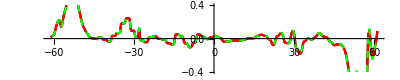

```mathematica
ddd=Total[#[[1]]phi2[[#[[2]];;#[[3]],64]]&/@{{-1,5,-1},{16,4,-2},{-30,3,-3},{16,2,-4},{-1,1,-5}}]/12;
ListLinePlot[{
Transpose[{x3[[2;;-2]],Differences[n^2 phi1[[;;,64]],2]}]
,Transpose[{x3[[2;;-2]],Differences[phi2[[;;,64]],2]}]
,Transpose[{x3[[3;;-3]],ddd}]
},ImageSize->Full,AspectRatio->0.2,PlotRange->{All,{-1,1}0.4},PlotLegends->{"input","output","4th order"},PlotStyle->{{Black,Thick},{Red,Thin},{Green,Thin,Dashed}}]
```

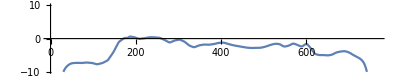

-Graphics-

```mathematica
ListLinePlot[Differences[n^2 phi1[[;;,64]],1],ImageSize->Full,AspectRatio->0.2,PlotRange->{All,{-1,1}10}]
ListLinePlot[Differences[phi2[[;;,64]],1],ImageSize->Full,AspectRatio->0.2,PlotRange->{All,{-1,1}10}]
```

```mathematica
altref=300;
x1i=(Position[#,Min[#]]&@Abs[x1-altref])[[1,1]];
eastref=0;
x2i=(Position[#,Min[#]]&@Abs[x2-eastref])[[1,1]];
j1A=Import["\\\\Dartfs-hpc\\rc\\lab\\L\\LynchK\\public_html\\Gemini3D\\"<>run<>"\\"<>rA<>"\\20170302_"<>ToString[t]<>".000000.h5","/J1all"][[;;,x2i,-1]] 10^6;
j1B=Import["\\\\Dartfs-hpc\\rc\\lab\\L\\LynchK\\public_html\\Gemini3D\\"<>run<>"\\"<>rB<>"\\20170302_"<>ToString[t]<>".000000.h5","/J1all"][[;;,x2i,-1]] 10^6;
```

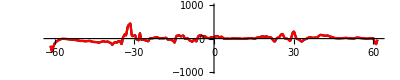

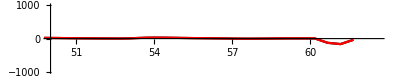

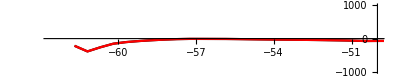

```mathematica
lim={-1,1}1000;
ListLinePlot[{Transpose[{x3,j1A}],Transpose[{x3,j1B}]},PlotLegends->{rA,rB},PlotStyle->{{Black,Thick},{Red,Thin}},ImageSize->Full,AspectRatio->0.2,PlotRange->{All,lim}]
ListLinePlot[{Transpose[{x3,j1A}],Transpose[{x3,j1B}]},PlotLegends->{rA,rB},PlotStyle->{{Black,Thick},{Red,Thin}},ImageSize->Full,AspectRatio->0.2,PlotRange->{{50,62.6},lim}]
ListLinePlot[{Transpose[{x3,j1A}],Transpose[{x3,j1B}]},PlotLegends->{rA,rB},PlotStyle->{{Black,Thick},{Red,Thin}},ImageSize->Full,AspectRatio->0.2,PlotRange->{{-62.6,-50},lim}]
```

```mathematica
j1all=Import["\\\\Dartfs-hpc\\rc\\lab\\L\\LynchK\\public_html\\Gemini3D\\"<>run<>"\\"<>rA<>"\\20170302_"<>ToString[t]<>".000000.h5","/J1all"][[;;,;;,-1]] 10^6;
```

```mathematica
ListPlot3D[j1all,AspectRatio->{1,1,0.1},ImageSize->Large,PlotRange->All]
```

-Graphics3D-

```mathematica
ne=Import["\\\\Dartfs-hpc\\rc\\lab\\L\\LynchK\\public_html\\Gemini3D\\"<>run<>"\\"<>rA<>"\\20170302_"<>ToString[t]<>".000000.h5","/nsall"][[7,;;,x2i,;;]];
```

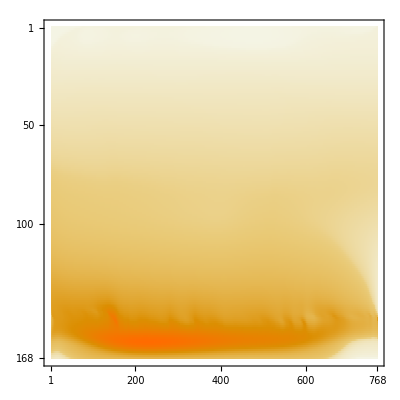

```mathematica
MatrixPlot[Reverse[Transpose[ne]],AspectRatio->1]
```

```mathematica
(*j1A[[-3]]
j1B[[-3]]*)
```

```mathematica
(*ListLinePlot[Transpose[{{360,365,370,375,380,390,405},{0,-38,-285,-1207,-2266,-3270,-3400}}],PlotMarkers->{Automatic, 10}]
ListLinePlot[Transpose[{{360,365,370,375,380,390,405},{0,-20,-76,-129,-239,-321,-387}}],PlotMarkers->{Automatic, 10}]*)
```

```mathematica
(*neA=Import["\\\\Dartfs-hpc\\rc\\lab\\L\\LynchK\\public_html\\Gemini3D\\"<>run<>"\\"<>rA<>"\\20170302_"<>ToString[t]<>".000000.h5","/nsall"][[7,;;,x2i,x1i]];
neB=Import["\\\\Dartfs-hpc\\rc\\lab\\L\\LynchK\\public_html\\Gemini3D\\"<>run<>"\\"<>rB<>"\\20170302_"<>ToString[t]<>".000000.h5","/nsall"][[7,;;,x2i,x1i]];*)
```

```mathematica
(*ListLinePlot[{Transpose[{x3,Log10[neA]}],Transpose[{x3,Log10[neB]}]},PlotLegends->{rA,rB},PlotStyle->{{Black,Thick},{Red,Thin}},ImageSize->Full,AspectRatio->0.2,PlotRange->{All,All}]
ListLinePlot[{Transpose[{x3,Log10[neA]}],Transpose[{x3,Log10[neB]}]},PlotLegends->{rA,rB},PlotStyle->{{Black,Thick},{Red,Thin}},ImageSize->Full,AspectRatio->0.2,PlotRange->{{50,62.6},All}]
ListLinePlot[{Transpose[{x3,Log10[neA]}],Transpose[{x3,Log10[neB]}]},PlotLegends->{rA,rB},PlotStyle->{{Black,Thick},{Red,Thin}},ImageSize->Full,AspectRatio->0.2,PlotRange->{{-62.6,-50},All}]*)
```

```mathematica
(*Log10[neA[[-1]]]
Log10[neB[[-1]]]*)
```

```mathematica
(*ListLinePlot[Transpose[{{360,365,370,375,390,405},{9.52,10.50,11.45,12.05,12.42,12.43}}],PlotMarkers->{Automatic, 10}]
ListLinePlot[Transpose[{{360,365,370,375,390,405},{9.52,10.02,10.72,10.99,11.47,11.55}}],PlotMarkers->{Automatic, 10}]*)
```

```mathematica
v2A=Import["\\\\Dartfs-hpc\\rc\\lab\\L\\LynchK\\public_html\\Gemini3D\\"<>run<>"\\"<>rA<>"\\20170302_"<>ToString[t]<>".000000.h5","/v2avgall"][[;;,x2i,x1i]];
v2B=Import["\\\\Dartfs-hpc\\rc\\lab\\L\\LynchK\\public_html\\Gemini3D\\"<>run<>"\\"<>rB<>"\\20170302_"<>ToString[t]<>".000000.h5","/v2avgall"][[;;,x2i,x1i]];
v3A=Import["\\\\Dartfs-hpc\\rc\\lab\\L\\LynchK\\public_html\\Gemini3D\\"<>run<>"\\"<>rA<>"\\20170302_"<>ToString[t]<>".000000.h5","/v3avgall"][[;;,x2i,x1i]];
v3B=Import["\\\\Dartfs-hpc\\rc\\lab\\L\\LynchK\\public_html\\Gemini3D\\"<>run<>"\\"<>rB<>"\\20170302_"<>ToString[t]<>".000000.h5","/v3avgall"][[;;,x2i,x1i]];
```

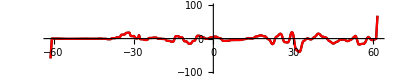

```mathematica
ListLinePlot[{Transpose[{x3[[2;;]],Differences[v2A]/Table[x2[[-1]]-x2[[-2]],Length[x3]-1]+Differences[v3A]/Differences[x3]}],Transpose[{x3[[2;;]],Differences[v2B]/Table[x2[[-1]]-x2[[-2]],Length[x3]-1]+Differences[v3B]/Differences[x3]}]},PlotLegends->{rA,rB},PlotStyle->{{Black,Thick},{Red,Thin}},ImageSize->Full,AspectRatio->0.2,PlotRange->{All,{-1,1}100}]
```

```mathematica
phiDS=phi[[;;;;n,;;;;n]];
E2=-Transpose[Differences[Transpose[phiDS[[;;-2,;;]]]]]/(x2[[64]]-x2[[63]]);
E3=-Differences[phiDS[[;;,;;-2]]]/(x3[[64]]-x3[[63]]);
Bmag=0.00005;
v2=-E3/Bmag/1000;
v3=E2/Bmag/1000;
```

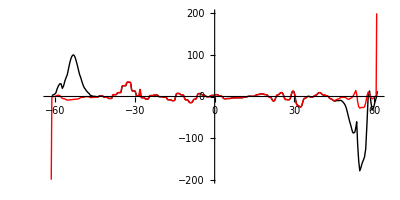

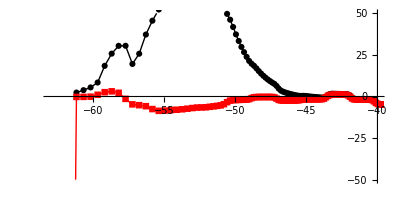

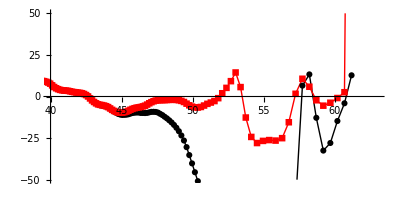

```mathematica
ListLinePlot[{Transpose[{x3[[2;;-2]],Differences[v2[[;;,x2i]]]}],Transpose[{x3[[;;-2]],Differences[v2A]}]},PlotStyle->{{Black,Thick},{Red,Thin}},ImageSize->Full,AspectRatio->0.5,PlotRange->{All,{-1,1}200}]
ListLinePlot[{Transpose[{x3[[2;;-2]],Differences[v2[[;;,x2i]]]}],Transpose[{x3[[;;-2]],Differences[v2A]}]},PlotStyle->{{Black,Thick},{Red,Thin}},ImageSize->Full,AspectRatio->0.5,PlotRange->{{-63,-40},{-1,1}50},PlotMarkers->Automatic]
ListLinePlot[{Transpose[{x3[[2;;-2]],Differences[v2[[;;,x2i]]]}],Transpose[{x3[[;;-2]],Differences[v2A]}]},PlotStyle->{{Black,Thick},{Red,Thin}},ImageSize->Full,AspectRatio->0.5,PlotRange->{{40,63},{-1,1}50},PlotMarkers->Automatic]
```

```mathematica
{512/5,768/7.5,1024/18}*1.
```

{102.4,102.4,56.8889}

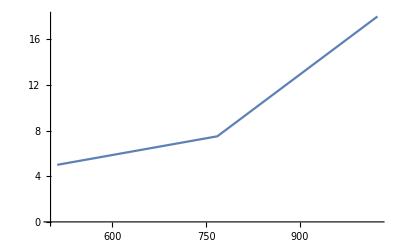

```mathematica
ListLinePlot[{{512,5},{768,7.5},{1024,18}}]
```

```mathematica
l=Table[Subscript[a, i],{i,1,10}];
d2=Differences[l,2];
a1=Solve[d2[[1]]==d2[[2]],Subscript[a, 1]][[1,1,2]]
lA=l/.Subscript[a, 1]->a1;
d1A=Differences[lA,1];
a2=Solve[d1A[[1]]==d1A[[2]],Subscript[a, 2]][[1,1,2]]
lB=lA/.Subscript[a, 2]->a2//FullSimplify;
lB//TableForm
```

3 a_2-3 a_3+a_4

2 a_3-a_4

3 a_3-2 a_4
2 a_3-a_4
a_3
a_4
a_5
a_6
a_7
a_8
a_9
a_10

```mathematica
d2=Differences[lB,2];
a10=Solve[d2[[-1]]==d2[[-2]],Subscript[a, 10]][[1,1,2]]
lC=lB/.Subscript[a, 10]->a10;
d1A=Differences[lC,1];
a9=Solve[d1A[[-1]]==d1A[[-2]],Subscript[a, 9]][[1,1,2]]
lD=lC/.Subscript[a, 9]->a9//FullSimplify;
lD//TableForm
```

a_7-3 a_8+3 a_9

-a_7+2 a_8

3 a_3-2 a_4
2 a_3-a_4
a_3
a_4
a_5
a_6
a_7
a_8
-a_7+2 a_8
-2 a_7+3 a_8

```mathematica
Differences[lD,1]//TableForm
Differences[lD,2]//TableForm
```

-a_3+a_4
-a_3+a_4
-a_3+a_4
-a_4+a_5
-a_5+a_6
-a_6+a_7
-a_7+a_8
-a_7+a_8
-a_7+a_8

0
0
a_3-2 a_4+a_5
a_4-2 a_5+a_6
a_5-2 a_6+a_7
a_6-2 a_7+a_8
0
0